```mathematica
(*简单相关*)
```

```mathematica
x[t_]:=Sin[5t]/((t-0.5)^2+0.05);y[t_]:=(0.2x[t-10]+RandomReal[]-0.5)*UnitStep[(t-8)(12-t)];
```

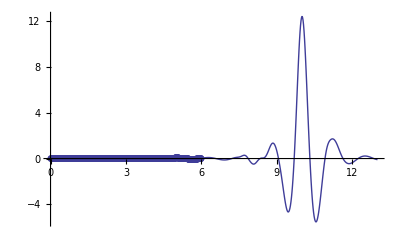

```mathematica
R={};s=Table[{t,y[t]},{t,-5,15,0.02}];
s=Interpolation[s];
Do[c=NIntegrate[s[t]*x[t-τ],{t,8,12}];AppendTo[R,{τ,c}],{τ,0,13,0.02}]
ListLinePlot[R,PlotRange->All,AxesLabel->{"τ","R"},PlotMarkers->Automatic]
```

```mathematica
Clear[x,y,R,c,s]
```

```mathematica
(*复杂相关*)
```

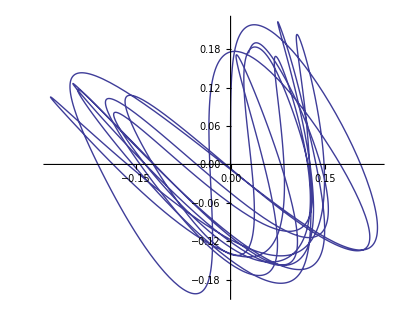

```mathematica
g=9.8;k=0.5;m1=0.1;m2=0.05;L1=1;L2=0.2;tm=20.0;initial1={0,0.8/L1};initial2={0,0.0,-(L1+L2),0};
temp=2 L1 (y2[t] Cos[θ[t]]-x2[t] Sin[θ[t]]);
L=Sqrt[x2[t]^2+y2[t]^2+L1^2+temp];eqs={θ''[t]==-(g/L1) Sin[θ[t]]+(Cos[θ[t]]*x2[t]+Sin[θ[t]]*y2[t]) (1-L2/L)*k/(m1 L1),x2''[t]==-(k/m2) (1-L2/L) (x2[t]-L1 Sin[θ[t]]),y2''[t]==-(k/m2) (1-L2/L) (y2[t]+L1 Cos[θ[t]])-g,θ[0]==initial1[[1]],θ'[0]==initial1[[2]],x2[0]==initial2[[1]],x2'[0]==initial2[[2]],y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};s=NDSolve[eqs,{θ,x2,y2},{t,0,tm},MaxSteps->∞];
{θ,x2,y2}={θ,x2,y2}/.s[[1]];
ParametricPlot[{x2[t],θ[t]},{t,0,tm},PlotPoints->1000,AxesOrigin->{0,0},AxesLabel->{"x_2,θ"}]
```

```mathematica
Clear[L1,L2,g,k,m1,m2,tm,initial1,initial2,L,eqs,θ,x2,y2,temp,s]
```

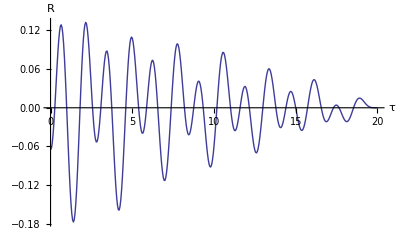

```mathematica
g=9.8;k=0.5;m1=0.1;m2=0.05;L1=1;L2=0.2;tm=20.0;initial1={0,0.8/L1};initial2={0,0.0,-(L1+L2),0};
temp=2 L1 (y2[t] Cos[θ[t]]-x2[t] Sin[θ[t]]);
L=Sqrt[x2[t]^2+y2[t]^2+L1^2+temp];eqs={θ''[t]==-(g/L1) Sin[θ[t]]+(Cos[θ[t]]*x2[t]+Sin[θ[t]]*y2[t]) (1-L2/L)*k/(m1 L1),x2''[t]==-(k/m2) (1-L2/L) (x2[t]-L1 Sin[θ[t]]),y2''[t]==-(k/m2) (1-L2/L) (y2[t]+L1 Cos[θ[t]])-g,θ[0]==initial1[[1]],θ'[0]==initial1[[2]],x2[0]==initial2[[1]],x2'[0]==initial2[[2]],y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};s=NDSolve[eqs,{θ,x2,y2},{t,0,tm},MaxSteps->∞];
{θ,x2,y2}={θ,x2,y2}/.s[[1]];

R={};
s1[t_]:=θ[t]UnitStep[t(tm-t)];
s2[t_]:=x2[t]UnitStep[t(tm-t)];
Do[c=NIntegrate[s1[t]*s2[t-τ],{t,0,tm}];AppendTo[R,{τ,c}],{τ,0,tm,0.05}]

ListLinePlot[R,PlotRange->All,AxesLabel->{"τ","R"}]
```

```mathematica
Clear[R,s1,s2,c]
```

```mathematica
(*相关运算函数*)
```

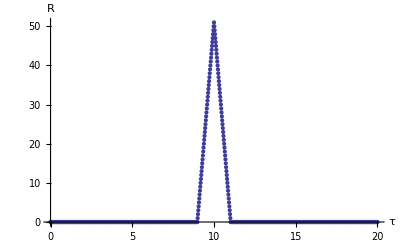

```mathematica
y[t_]:=UnitStep[(t-10)(11-t)];
x[t_]:=UnitStep[t(1-t)];
sample=1000;tm=20.0;
ysqs=Table[y[t],{t,0,tm,tm/sample}];
xsqs=Table[x[t],{t,0,tm,tm/sample}];
c=ListCorrelate[xsqs,ysqs,1,0];
Len=Length[c];
c=Table[{((j-1)tm)/sample,c[[j]]},{j,Len}];
ListPlot[c,PlotRange->All,AxesLabel->{"τ","R"}]
```

```mathematica
Clear[x,y,xsqs,ysqs,c,sample,Len]
```

```mathematica
(*正弦信号*)
```

```mathematica
(x0*y0)/T*Integrate[Sin[ω*t+ϕ1]*Sin[ω*(t-τ)+ϕ2],{t,-T/2,T/2}]
```

```mathematica
FullSimplify[(x0 y0 (2 T ω Cos[ϕ1-ϕ2+τ ω]-Sin[ϕ1+ϕ2+T ω-τ ω]+Sin[ϕ1+ϕ2-(T+τ) ω]))/(4 T ω),Assumptions->T ω==2π]
```

1/2 x0 y0 Cos[ϕ1-ϕ2+τ ω]

```mathematica
(*提取测量信号*)
```

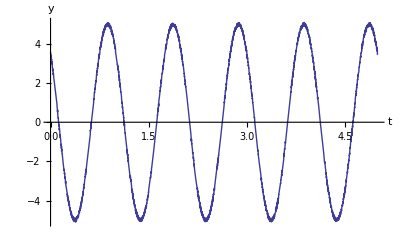

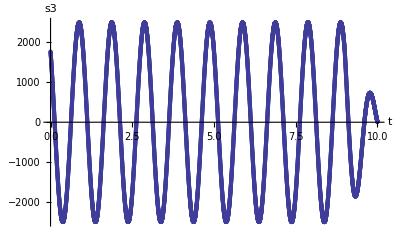

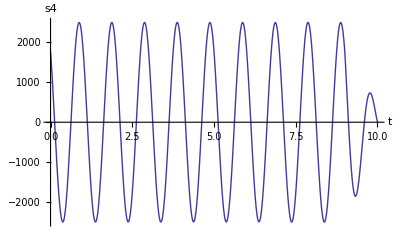

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

```mathematica
x0=1;ω=2π/T;T=1.0;ϕ1=π/4;y0=5;sample=1000;
x[t_]:=x0 Cos[ω*t];
y[t_]:=y0 Cos[ω*t+ϕ1]+(Random[]-0.5)/5;
Plot[y[t],{t,0,5},AxesLabel->{"t","y"}]
s1=Table[x[((j-1)*T)/sample],{j,sample}];
s2=Table[y[((j-1)*T)/sample],{j,10sample}];
s=ListCorrelate[s1,s2,1,0];
Len=Length[s];
s3=Table[{((j-1)*T)/sample,s[[j]]},{j,Len}];
ListPlot[s3,AxesLabel->{"t","s3"}]
s4=Interpolation[s3];
Plot[s4[t],{t,0,((Len-1)T)/sample},AxesLabel->{"t","s4"}]
Y=FindMaximum[s4[t],{t,0.8}];
s5[t_]:=Y Cos[ω*t];
Plot[s5[t],{t,0,((Len-1)T)/sample},AxesLabel->{"t","s5"}]
```

```mathematica
Clear[ϕ1,T,ω,x0,y0,x,y,sample,s1,s2,s3,s4,s5,Y,s]
```